```mathematica
(*Use HoldComplete[FullForm[...]] to see underlying code *)

K1 = 1;
K3= 1.2;
K2= 3.0;
Subscript[ϕ, 0]= Pi/4;

g[x_, K_]:=Cos[x]^2(K*Cos[x]^2+ K3*Sin[x]^2)
f[x_]:= K1*Cos[x]^2+ K3*Sin[x]^2

G[u_, θ_, K_]:=√(f[u]/(g[u, K](g[u, K]-g[θ, K])))
```

```mathematica
g[.5, 3.0]
```

1.99182

```mathematica
W[θ_, K_]:=Chop[Sqrt[g[θ, K]]NIntegrate[G[u,θ, K], {u, 0,θ}] ,0.0001] - Subscript[ϕ, 0]
```

```mathematica
W[.7, K2]
```

0.0103002

```mathematica
Subscript[M, s][K_]:= th /. FindRoot[W[th, K], {th,0.6, 0, 1.4}, Evaluated->False]
Subscript[M, m][K_]:= th /. FindRoot[W[th, K], {th,0.8, 0, 1.0}, Evaluated->False]
Subscript[M, l][K_]:= th /. FindRoot[W[th, K], {th,0.8, 0, 1.4}, Evaluated->False]
Subscript[M, ll][K_]:= th /. FindRoot[W[th, K], {th,0.9, 0, 1.0}, Evaluated->False]
```

```mathematica
Subscript[R, s] = Range[2.6, 2.8, 0.01];
Subscript[R, m] = Range[2.8, 3.1, 0.01];
Subscript[R, l]= Range[3.1, 3.25, 0.01];
Subscript[R, ll]= Range[3.25, 3.6, 0.01];
```

```mathematica
Subscript[M, s][2.6]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

0.0270407

```mathematica
Subscript[MMap, s] = Map[Subscript[M, s], Subscript[R, s]];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

```mathematica
Subscript[MMap, m] = Map[Subscript[M, m], Subscript[R, m]];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

```mathematica
Subscript[MMap, l]= Map[Subscript[M, l], Subscript[R, l]];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

```mathematica
Subscript[MMap, ll]= Map[Subscript[M, ll], Subscript[R, ll]];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

```mathematica
(*p1 = Plot[M[Subscript[K, l]], {Subscript[K, l], 2.9, 3.1}, PlotStyle->{Red, Thickness[0.01]}]*)
```

```mathematica
Subscript[MX, s] =Partition[Riffle[Subscript[R, s], Subscript[MMap, s]],2];
```

```mathematica
Subscript[Mx, s] = Interpolation[Subscript[MX, s]];
```

```mathematica
Subscript[MX, m] =Partition[Riffle[Subscript[R, m], Subscript[MMap, m]],2];
```

```mathematica
Subscript[Mx, m] = Interpolation[Subscript[MX, m]];
```

```mathematica
Subscript[MX, l] =Partition[Riffle[Subscript[R, l], Subscript[MMap, l]],2];
```

```mathematica
Subscript[Mx, l] = Interpolation[Subscript[MX, l]];
```

```mathematica
Subscript[MX, ll] =Partition[Riffle[Subscript[R, ll], Subscript[MMap, ll]],2];
```

```mathematica
Subscript[Mx, ll] = Interpolation[Subscript[MX, ll]];
```

```mathematica
p1= Plot[Subscript[Mx, s][x], {x, 2.6, 2.8}, PlotStyle->{Red, Thickness[0.008]}];
p2= Plot[Subscript[Mx, m][x], {x, 2.8, 3.1}, PlotStyle->{Red, Thickness[0.008]}];
p3 = Plot[Subscript[Mx, l][x], {x, 3.1, 3.25}, PlotStyle->{Red, Thickness[0.008]}];
p4 = Plot[Subscript[Mx, ll][x], {x, 3.25, 3.6}, PlotStyle->{Red, Thickness[0.008]}];
```

```mathematica
p5= Plot[-Subscript[Mx, s][x], {x, 2.6, 2.8}, PlotStyle->{Blue, Thickness[0.008]}];
p6= Plot[-Subscript[Mx, m][x], {x, 2.8, 3.1}, PlotStyle->{Blue, Thickness[0.008]}];
p7 = Plot[-Subscript[Mx, l][x], {x, 3.1, 3.25}, PlotStyle->{Blue, Thickness[0.008]}];
p8 = Plot[-Subscript[Mx, ll][x], {x, 3.25, 3.6}, PlotStyle->{Blue, Thickness[0.008]}] ;
```

```mathematica
p9 = Plot[0*Subscript[K, l], {Subscript[K, l], 1.5, 3.6}, PlotStyle->{Magenta, Thickness[0.008]}];
```

```mathematica
USol = {{1.6, 3.225364948183729*10^-17},{1.8, 1.288423003633209*10^-15},{2.0, 3.865806057713935*10^-15},{2.2, -8.08692980178347*10^-15},{2.4, 1.724586023683678*10^-14},{2.6, -0.000112656690967150},{2.8, 2.877959896458964*10^-14},{3.0, 1.406649147664742*10^-14},{3.2, -6.419914116299728*10^-15},{3.4, 6.077731393631001*10^-15},{3.6,4.69791551929853*10^-15}};
PosFreed = {{2.8, 0.495642550984164},{3.0, 0.6605430012875417},{3.2, 0.767312308722812},{3.4, 0.8448071792814332},{3.6,0.9045248211233998}};
NegFreed = {{2.8, -0.4956425509841638},{3.0, -0.6605430012875403},{3.2, -0.7673123087228108},{3.6, -0.904524821123399}};
markers= Graphics[Disk[]];
l1 = ListPlot[USol, PlotMarkers->{"*", 30}, PlotStyle->Black];
l2 = ListPlot[PosFreed, PlotMarkers->{"*", 30}, PlotStyle->Purple];
l3 = ListPlot[NegFreed, PlotMarkers->{"*", 30}, PlotStyle->Darker[Green,.7]];
```

```mathematica
(*This array holds the locations of the ticks*)
xtickloc = Range[1.5, 3.6, 0.1];
(*This function determines the size of the ticks, currently if they are divisible evenly by 0.5
the tick mark is slighly larger*)
gx[x_]:= If[Abs[Mod[x, 0.5]]<10^-9|| Abs[Mod[x, 0.5]]==0.5, ToString[Chop[x]], ""];
xlab = Map[gx, xtickloc];
fx[x_] := If[Abs[Mod[x, 0.5]]<10^-9|| Abs[Mod[x, 0.5]]==0.5, {0.014, 0}, {0.01, 0}];
xticksize = Map[fx, xtickloc] ;
xticks = Transpose[{xtickloc, xlab, xticksize}];
(*This array holds the locations of the ticks*)
ytickloc = Range[-1.2, 1.2, 0.1];
(*This function determines the size of the ticks, currently if they are divisible evenly by 0.5
the tick mark is slighly larger*)
gy[x_]:= If[Abs[Mod[x, 0.5]]<10^-9|| Abs[Mod[x, 0.5]]==0.5,ToString[Chop[x]] ,""];
ylab = Map[gy, ytickloc];
fy[x_] := If[Abs[Mod[x, 0.5]]<10^-9|| Abs[Mod[x, 0.5]]==0.5, {0.014, 0}, {0.01, 0}];
yticksize = Map[fy, ytickloc] ;
yticks = Transpose[{ytickloc, ylab, yticksize}];
```

```mathematica
Needs["PlotLegends`"];
```

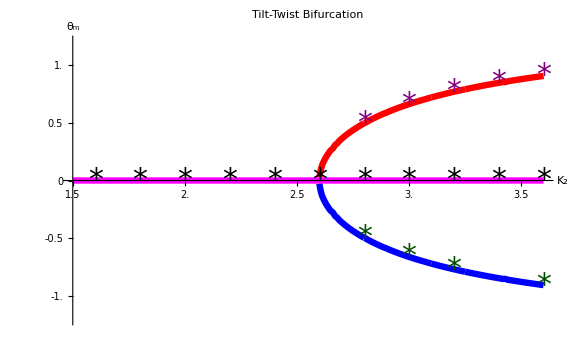

```mathematica
ShowLegend[Show[p1,p2,p3,p4, p5, p6, p7, p8, p9, l1, l2, l3, PlotRange-> {{1.5, 3.6},{-1.2,1.2}}, AxesOrigin->{1.5,0}, AxesLabel-> {Subscript[K, 2], Subscript[θ, m]}, TicksStyle-> Thickness[0.003], AxesStyle-> Thickness[0.003],LabelStyle-> Directive[Bold, FontFamily-> "Helvetica", FontSize-> 18], ImageSize->Large,PlotLabel-> Style["Tilt-Twist Bifurcation", "Helvetica", 20], Ticks-> {xticks,yticks}],{{{Graphics[{Magenta, Thickness[0.3],Line[{{0,0},{2.0,0}}]}],Style["Twist", 14, Bold, FontFamily->"Helvetica"]},{Graphics[{Red, Thickness[0.3],Line[{{0,0},{2.0,0}}]}],Style["Tilt-Pos",14, Bold, FontFamily->"Helvetica"]}, {Graphics[{Blue, Thickness[0.3],Line[{{0,0},{2.0,0}}]}],Style["Tilt-Neg",14, Bold, FontFamily->"Helvetica"]}}, LegendPosition->{-0.7,0.25},LegendSize->{0.38,0.2},LegendShadow->False, LegendTextSpace-> 3, LegendBorder->None}]
```

```mathematica
(*Export["/Users/Emersodb/Desktop/TiltTwistBifurcationLeg.png",%2010,  ImageResolution-> 300]*)
```

```mathematica
(********************************** ENERGY PLOT **********************************)
```

```mathematica
b[M_, K_]:= Chop[2Sqrt[g[M, K]]NIntegrate[Sqrt[(f[u]g[u, K])/(g[u, K]-g[M, K])],{u, 0, M}], 0.0001];
Subscript[Eval, s]=Partition[Riffle[Subscript[MMap, s], Subscript[R, s]],2];
Subscript[b, s]=Apply[b, Subscript[Eval, s],{1}];
Subscript[Eval, m]=Partition[Riffle[Subscript[MMap, m], Subscript[R, m]],2];
Subscript[b, m]=Apply[b, Subscript[Eval, m],{1}];
Subscript[Eval, l]=Partition[Riffle[Subscript[MMap, l], Subscript[R, l]],2];
Subscript[b, l]=Apply[b, Subscript[Eval, l],{1}];
Subscript[Eval, ll]=Partition[Riffle[Subscript[MMap, ll], Subscript[R, ll]],2];
Subscript[b, ll]=Apply[b, Subscript[Eval, ll],{1}];
```

```mathematica
Subscript[gval, s] =Apply[g, Subscript[Eval, s],{1}] ;
Subscript[gval, m] =Apply[g, Subscript[Eval, m],{1}] ;
Subscript[gval, l] =Apply[g, Subscript[Eval, l],{1}] ;
Subscript[gval, ll] =Apply[g, Subscript[Eval, ll],{1}] ;
```

```mathematica
Eng[b_, g_]:=b^2/(2g);
```

```mathematica
Subscript[Eng, s]= Apply[Eng, Partition[Riffle[Subscript[b, s],Subscript[gval, s]],2],{1}];
Subscript[Eng, m]=Apply[Eng, Partition[Riffle[Subscript[b, m],Subscript[gval, m]],2],{1}];
Subscript[Eng, l]=Apply[Eng, Partition[Riffle[Subscript[b, l],Subscript[gval, l]],2],{1}];
Subscript[Eng, ll]=Apply[Eng, Partition[Riffle[Subscript[b, ll],Subscript[gval, ll]],2],{1}];
```

```mathematica
Subscript[Engx, s]=Interpolation[Partition[Riffle[Subscript[R, s],Subscript[Eng, s]],2]];
Subscript[Engx, m]=Interpolation[Partition[Riffle[Subscript[R, m],Subscript[Eng, m]],2]];
Subscript[Engx, l]=Interpolation[Partition[Riffle[Subscript[R, l],Subscript[Eng, l]],2]];
Subscript[Engx, ll]=Interpolation[Partition[Riffle[Subscript[R, ll],Subscript[Eng, ll]],2]];
```

```mathematica
EngP1 = Plot[Subscript[Engx, s][x], {x, 2.6, 2.8}, PlotStyle->{Red, Thickness[0.008]}];
EngP2= Plot[Subscript[Engx, m][x], {x, 2.8, 3.1}, PlotStyle->{Red, Thickness[0.008]}];
EngP3 = Plot[Subscript[Engx, l][x], {x, 3.1, 3.25}, PlotStyle->{Red, Thickness[0.008]}];
EngP4 = Plot[Subscript[Engx, ll][x], {x, 3.25, 3.6}, PlotStyle->{Red, Thickness[0.008]}];
DegEng = Plot[2*x*(Subscript[ϕ, 0])^2, {x, 1.5, 3.6}, PlotStyle->{Magenta, Thickness[0.008]}];
```

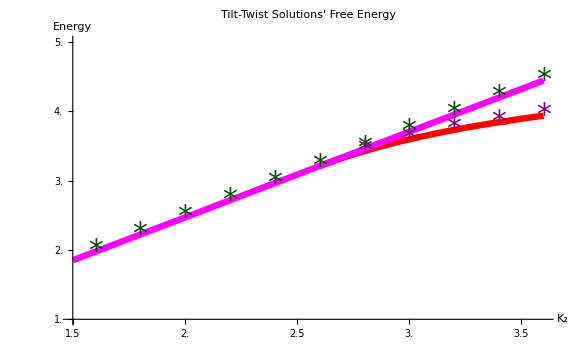

```mathematica
DegenEnergy = {{1.6, 1.973920880220467},{1.8, 2.220660990249596},{2.0, 2.467401100276002},{2.2, 2.714141210307635},{2.4, 2.960881320330945},{2.6, 3.207621441959183},{2.8, 3.454361540383804},{3.0, 3.701101650419396},{3.2, 3.947841760440934},{3.4, 4.194581870476204},{3.6,4.4413219804991912 }};
FreedEnergy = {{2.8, 3.423958574404506},{3.0, 3.592936587816029},{3.2, 3.728796566217099},{3.4,3.840627347096749},{3.6, 3.934471881014743}};
markers= Graphics[Disk[]];
en1 = ListPlot[DegenEnergy, PlotMarkers->{"*", 30}, PlotStyle->Darker[Green,.7]];
en2 = ListPlot[FreedEnergy, PlotMarkers->{"*", 30}, PlotStyle->Purple];

(*This array holds the locations of the ticks*)
xtickloc2 = Range[1.5, 3.6, 0.1];
(*This function determines the size of the ticks, currently if they are divisible evenly by 0.5
the tick mark is slighly larger*)
gx2[x_]:= If[Abs[Mod[x, 0.5]]<10^-9|| Abs[Mod[x, 0.5]]==0.5, ToString[Chop[x]], ""];
xlab2 = Map[gx2, xtickloc2];
fx2[x_] := If[Abs[Mod[x, 0.5]]<10^-9|| Abs[Mod[x, 0.5]]==0.5, {0.014, 0}, {0.01, 0}];
xticksize2= Map[fx2, xtickloc2] ;
xticks2 = Transpose[{xtickloc2, xlab2, xticksize2}];
(*This array holds the locations of the ticks*)
ytickloc2= Range[0, 5.0, 0.2];
(*This function determines the size of the ticks, currently if they are divisible evenly by 0.5
the tick mark is slighly larger*)
gy2[x_]:= If[Abs[Mod[x, 1.0]]<10^-9|| Abs[Mod[x, 1.0]]==1.0,ToString[Chop[x]] ,""];
ylab2 = Map[gy2, ytickloc2];
fy2[x_] := If[Abs[Mod[x, 1.0]]<10^-9|| Abs[Mod[x, 1.0]]==1.0, {0.014, 0}, {0.01, 0}];
yticksize2 = Map[fy2, ytickloc2] ;
yticks2 = Transpose[{ytickloc2, ylab2, yticksize2}];

ShowLegend[Show[ EngP1,EngP2, EngP3, EngP4, DegEng,en1, en2,PlotRange-> {{1.5, 3.6},{1.0,5.0}}, AxesOrigin->{1.5,1.0}, AxesLabel-> {Subscript[K, 2], "Energy"}, TicksStyle-> Thickness[0.003], AxesStyle-> Thickness[0.003],LabelStyle-> Directive[Bold, FontFamily-> "Helvetica", FontSize-> 18], ImageSize->Large,PlotLabel-> Style["Tilt-Twist Solutions' Free Energy", "Helvetica", 20],Ticks-> {xticks2,yticks2}],{{{Graphics[{Magenta, Thickness[0.2],Line[{{0.0,0},{1.5,0}}]}],Style["Twist", 14, Bold, FontFamily->"Helvetica"]}, {Graphics[{Red, Thickness[0.2],Line[{{0.0,0},{1.5,0}}]}],Style["Tilt",14, Bold, FontFamily->"Helvetica"]}}, LegendPosition->{-0.7,0.2},LegendSize->{0.42,0.2},LegendShadow->False, LegendTextSpace-> 3.5, LegendBorder->None}]
```

```mathematica
(*Export["/Users/Emersodb/Desktop/TiltTwistEnergyBifurcLeg.png",%183,  ImageResolution-> 300]*)
```

/Users/Emersodb/Desktop/TiltTwistEnergyBifurcLeg.png